## 4D STEM GUI Builder

This notebook loads a cropped, real-space (e.g., HAADF) image of the 4D STEM scan area, and displays a diffraction pattern from the location specified by the user’s mouse position on the HAADF image.

This is memory-intensive, but effective if you have no other GUI.

```mathematica
ClearAll["*Global`"]
```

Save the notebook in the folder where you have exported your image series and set the directory to the same.

```mathematica
SetDirectory[ NotebookDirectory[]]
```

E:\4D STEM project\TEM images\07 July 2018

This notebook imports entire datasets of diffraction patterns, e.g., 2500 .tif files. These images should exist in a folder. Here, I have three datasets in folders labeled “Series 1”, “Series 2”, and “Series 3”. We will make a path list to easily import all images later:

```mathematica
paths=Table[Directory[]<>"\\Series "<>ToString [i], {i,3}]
```

```mathematica
{"E:\\4D STEM project\\TEM images\\07 July 2018\\Series 1","E:\\4D STEM project\\TEM images\\07 July 2018\\Series 3","E:\\4D STEM project\\TEM images\\07 July 2018\\Series 3"}
```

Each folder has the cropped, real-space HAADF image from the 4D STEM scan area, labeled “Capture.png”. Import them here:

```mathematica
maps=Table[Import["Capture.png", Path-> paths⟦i⟧],{i,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

Create an empty 2D array using the same dimensions as your scan (here, 50 by 50 steps) which will be used to label axes and find the mouse position:

```mathematica
emptyset=ConstantArray[None,{50,50}];
```

Add the real-space image to the empty MatrixPlot using Prolog:

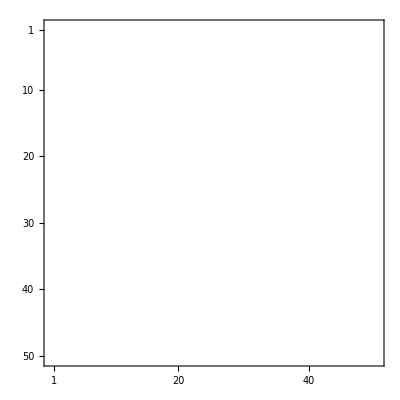

```mathematica
MatrixPlot[emptyset,Prolog->Inset[Image [maps⟦3⟧,ImageSize->315]]]
```

Get the image names and check that the right number of files exists in your path folders (here it should be 7500):

```mathematica
imageNames=FileNames["*tif",paths];
```

```mathematica
Length@imageNames
```

7500

Partition the image names according to the scan dimensions (here it is 50x50):

```mathematica
imageNameTable=Table[Partition[Partition[imageNames,2500]⟦i⟧,50],{i,3}];
```

Check an image; adjust contrast/brightness/gamma as needed:

```mathematica
ImageAdjust[Import[imageNameTable⟦3,2,17⟧],{.65,0.2,0.2}]
```

-Graphics-

This line would import all images from all paths, but beware, that would create a huge variable.

```mathematica
(*gigaImages=Table[ImageAdjust[Import[imageNameTable⟦i,j,k⟧],{.65,0.2,0.2}],{i,3},{j,50},{k,50}];*)
```

Instead we will import one series at a time. This may take a couple minutes.

```mathematica
series3=Table[ImageAdjust[Import[imageNameTable⟦3,j,k⟧],{.65,0.2,0.2}],{j,50},{k,50}];
```

Rename empty set as A for convenience:

```mathematica
A=emptyset;
```

Grab the scan dimensions (which you set earlier):

```mathematica
{n,m}=Dimensions@A;
```

Display the appropriate diffraction pattern for the mouse position on the real-space image:

```mathematica
DynamicModule[{trans,ij},trans[{x_,y_}]:={Clip[Floor[n-y]+1,{1,n}],Clip[Floor[x]+1,{1,m}]};
Row@{MatrixPlot[A,Prolog-> Inset[Image[maps⟦3⟧,ImageSize->454]],ImageSize->500],Dynamic[(ij=trans@MousePosition["Graphics",{0,0}])->Image[series3⟦Sequence@@ij⟧,ImageSize->454]]}]
```

You can easily grab individual diffraction patterns that you wish to inspect more closely:

```mathematica
toIndex={
series3⟦11,33⟧,
series3⟦17,37⟧,
series3⟦7,31⟧,
series3⟦37,50⟧,
series3⟦37,39⟧,
series3⟦33,19⟧
}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

And export them individually:

```mathematica
(*Table[Export["indexing_"<>ToString[i]<>".tif",toIndex⟦i⟧],{i,Length[toIndex]}]*)
```